```mathematica
OTC=ArrayReshape[Reverse[{542,482,553,493,551,628,691,710,696,635,641,648,707,601,582,603,595,598,673,586,507,418,373,299,283,259,220,197,169,142,128,111,100,96,94,88,81,80,72}],{39,1}];
```

```mathematica
dates=ArrayReshape[Reverse[DateRange[DateList["01 June 2017"],DateList["01 May 1998"],{-6,"Month"}]],{39,1,6}];
```

```mathematica
a=Join[dates,OTC,2];
```

```mathematica
img=DateListPlot[a,AxesLabel->{"$ trillion","A"},DateTicksFormat->{"MonthNameShort", "-", "YearShort"},FrameTicks->{{Automatic,Automatic},{{"June 1, 2001","June 1, 2005","June 1, 2009","June 1, 2013","June 1, 2017"},None}},ImageSize->Medium,FrameLabel->{,"$ Trillion"},PlotLegends->Placed[LineLegend[{"OTC Market Size"},LegendFunction->(Framed[#,RoundingRadius->0]&),LegendMargins->0],{{0.,0.0},{-0.45,-6}}],FrameStyle->Directive[FontSize->13],PlotStyle->Thickness[0.01])]
```

-Graphics-

```mathematica
Export["C:\\Users\\Miguel\\Documents\\GitHub\\Thesis\\Images\\OTC.eps",img,"eps"];
```

```mathematica
NotebookSave[]
```

```mathematica
Max[OTC]
```

710

```mathematica
K=1;
```

```mathematica
img2=Plot[{Max[x-K,0],Max[K-x,0]},{x,0,2},PlotStyle->{{Thickness[0.01],Dashing[{0.025,0.035}]},Thickness[0.01]},PlotLegends->Placed[LineLegend[{"call","put"},LegendFunction->(Framed[#,RoundingRadius->0]&),LegendMargins->0],{{0.,0.0},{-0.7,-3.4}}],ImageSize->Medium,AxesLabel->{"S(t)","Payoff"},Ticks->{{{K,"K"}},None},AxesStyle->Directive[FontSize->13]]
```

-Graphics-

```mathematica
Export["C:\\Users\\Miguel\\Documents\\GitHub\\Thesis\\Images\\Payoff.eps",img2,"eps"];
```

```mathematica
ClearAll["Global`*"]
```

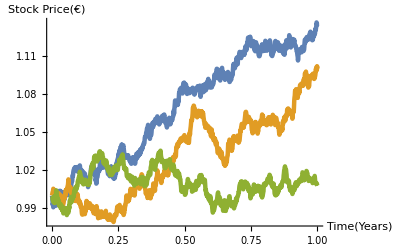

```mathematica
n=1000; (*Number of exercise points per year*)
T=1; (*Number of years in the contract*)
R=0.06;(*Yearly discount factor*)
sigma=0.05; (*Volatility of the underlying stock price*)
S0=1.; (*Initial stock price*)
dT=1/n; (*Time step duration*)
S1=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S1[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S1[[2,i+1]]=S1[[2,i]]+R*dT*S1[[2,i]]+sigma*S1[[2,i]]*dW[[1,i]];S1[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)
S2=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S2[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S2[[2,i+1]]=S2[[2,i]]+R*dT*S2[[2,i]]+sigma*S2[[2,i]]*dW[[1,i]];S2[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)
S3=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S3[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S3[[2,i+1]]=S3[[2,i]]+R*dT*S3[[2,i]]+sigma*S3[[2,i]]*dW[[1,i]];S3[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)
img3=ListPlot[{Transpose[S1],Transpose[S2],Transpose[S3]},AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.008]}]
```

```mathematica
(*If[True,
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\GBM.eps",img3,"eps"],];*)
```

```mathematica
If[True,
Export["C:\\Users\\Miguel\\Documents\\GitHub\\Thesis\\Images\\GBM.eps",img3,"eps"],];
```